```mathematica
f[x_]:=Piecewise[{{x (1-x), 0≤x≤1}, {-10^50, x<0∨x>1}}]
f[5]
```

-100000000000000000000000000000000000000000000000000

```mathematica
fs[xs_]:=fs[xs]=NMinimize[xs*x -f[x],x]//First
fs[0.5]
```

-0.0625

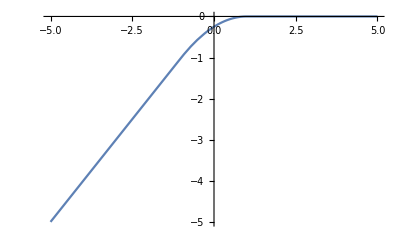

```mathematica
Plot[fs[xs],{xs,-5,5}]
```

```mathematica
Needs["NumericalCalculus`"]
fsd[xs_]:=(fs[xs+0.01]-fs[xs])/0.01
```

```mathematica
Plot[fsd[x],{x,-5,5}]
```

-Graphics-

```mathematica
Simplify[x(1-x)/2-(1-x)/2(1-(1-x)/2)]
```

-1/4 (-1+x)^2

```mathematica
fc[x_]:=Piecewise[{{x, x<-1}, {-(x-1)^2/4, -1≤x≤1}, {0, x>1}}]
```

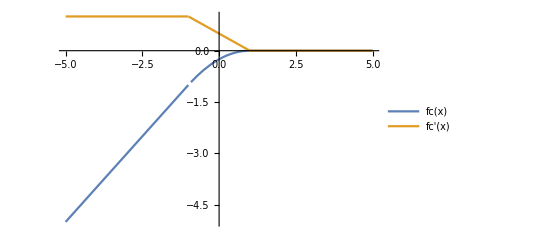

```mathematica
Plot[{fc[x],fc'[x]},{x,-5,5},PlotLegends->"Expressions"]
```